```mathematica
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]];
If[!MemberQ[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]],AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]]];
Print["Package path ",FindFile["GDCAnalysis3`"]];
Print["Package path ",FindFile["GDCComparisons`"]];
<<GDCAnalysis3`
<<GDCComparisons`
```

Package path /home/carla/GDC/DialecticalStructures/GDCAnalysis3.m

Package path /home/carla/GDC/DialecticalStructures/GDCComparisons.m

```mathematica
(*geändert 12/05/21: 
valNeu=Which[BooleanQ[val==GrayLevel[1]],
val,
val>thre,
col1,
val≤thre,
col2];*)
groupingFunc[val_,col1_,col2_, thre_]:=Module[{valNeu},
valNeu=Which[BooleanQ[val==GrayLevel[1]],
val,
val≥ thre,
col1,
val<thre,
col2];
Return[valNeu];
];

headMapGroupsEndo[dataH_,dataE_,tInd_, col1_,col2_,thre_]:=Module[{
dataEInd,dataHInd,names,
DLBe,MURe,LYEe,PHIe,SEDe,AUSe,DLBh,MURh,LYEh,PHIh,SEDh,AUSh,dataOut},
names=Keys[dataE];

dataEInd=Map[Function[z,Map[Function[y,Map[Function[x,groupingFunc[x,col1,Lighter[col1,0.8],thre]],dataE[z][[y]]]],Range[Length[dataE[z]]]]],names];
dataHInd=Map[Function[z,Map[Function[y,Map[Function[x,groupingFunc[x,col2,Lighter[col2,0.8],thre]],dataH[z][[y]]]],Range[Length[dataH[z]]]]],names];

DLBe=Insert[dataEInd[[1]][[All,tInd]],White,1];
MURe=Insert[dataEInd[[2]][[All,tInd]],White,2];
LYEe=Insert[dataEInd[[3]][[All,tInd]],White,3];
PHIe=Insert[dataEInd[[4]][[All,tInd]],White,4];
SEDe=Insert[dataEInd[[5]][[All,tInd]],White,5];
AUSe=Insert[dataEInd[[6]][[All,tInd]],White,6];

DLBh=Insert[dataHInd[[1]][[All,tInd]],White,1];
MURh=Insert[dataHInd[[2]][[All,tInd]],White,2];
LYEh=Insert[dataHInd[[3]][[All,tInd]],White,3];
PHIh=Insert[dataHInd[[4]][[All,tInd]],White,4];
SEDh=Insert[dataHInd[[5]][[All,tInd]],White,5];
AUSh=Insert[dataHInd[[6]][[All,tInd]],White,6];

dataOut={DLBh,
Catenate[{MURe[[1;;2]],MURh[[3;;]]}],
Catenate[{LYEe[[1;;3]],LYEh[[4;;]]}],
Catenate[{PHIe[[1;;4]],PHIh[[5;;]]}],
Catenate[{SEDe[[1;;5]],{SEDh[[6]]}}],
AUSe};

Return[dataOut];];

insetFunc[data_]:=Module[{box},
box=Text@Grid[Prepend[data,{Style["SIM PERS",15]," "}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Black,.9]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->{{Left,Center}},ItemSize->{{15,4}},Frame->Darker[Gray,.6],ItemStyle->10,Spacings->{Automatic,.8}];
Return[box];
];

(*dataH,dataE,names, len, dataMin, dataMax*)
groupingEndoTot[dH_,dE_, l_,nams_, dMin_,dMax_, thre_]:=Module[{data,plotsI,plotsF},

data=Map[headMapGroupsEndo[dH,dE,#,Orange,Blue,thre]&,Range[l]];

plotsI=
Map[Function[y,ArrayPlot[data[[y]], ColorFunction->"TemperatureMap",ImageSize->400,PlotLegends->Automatic,ImageMargins->10,PlotRange->{dMin,dMax},Frame->True,
FrameTicks->{{Map[Function[x,{x,nams[[x]]}],Range[6]],None},{Map[Function[x,{x,nams[[x]]}],Range[6]],None}}]],Range[l]];

(*{{Style["TIME",20],Style[ToString[tsAll[[#]]],20]}}*)
plotsF=Map[Show[plotsI[[#]],Graphics@Text[insetFunc[{{Style["THRE",15],Style[ToString[thre],15]},{Style["TIME",20],Style[ToString[tsStr[[#]]],20]}}],Offset[{150,10},Scaled[{0,1}]],{-1,-1}],PlotRangeClipping->False]&,Range[l]];

Return[plotsF];];
```

```mathematica
tsAR={0,1,2,3,4,5,6,7,8};tsBR={0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5};
tsALLRed=Drop[Union[tsAR,tsBR],2]
tsStr={"1b","2a","2b","3a","3b","4a","4b","5a","5b","6a","6b","7a","7b","8a","8b"}
tatCH=Map[Get[#]&,FileNames["/home/carla/GDC/POS/*.txt"]];
```

{1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8}

{1b,2a,2b,3a,3b,4a,4b,5a,5b,6a,6b,7a,7b,8a,8b}

```mathematica
(*First[persMixFunc["DLB"]],0,tsAR,*)
eDLBMUR=arrayFunc[First[persMixFunc["DLB"]],First[persMixFunc["MUR"]],0,tsALLRed, tatCH, "EVBK", "PEN"];
eDLBLYE=arrayFunc[First[persMixFunc["DLB"]],First[persMixFunc["LYE"]],0,tsALLRed, tatCH, "EVBK", "PEN"];
eDLBPHI=arrayFunc[First[persMixFunc["DLB"]],First[persMixFunc["PHI"]],2,tsALLRed, tatCH, "EVBK", "PEN"];
eDLBSED=arrayFunc[First[persMixFunc["DLB"]],First[persMixFunc["SED"]],4,tsALLRed, tatCH, "EVBK", "PEN"];
eDLBAUS=arrayFunc[First[persMixFunc["DLB"]],First[persMixFunc["AUS"]],10,tsALLRed, tatCH, "EVBK", "PEN"];
eMURLYE=arrayFunc[First[persMixFunc["MUR"]],First[persMixFunc["LYE"]],0,tsALLRed, tatCH, "EVBK", "PEN"];
eMURPHI=arrayFunc[First[persMixFunc["MUR"]],First[persMixFunc["PHI"]],2,tsALLRed, tatCH, "EVBK", "PEN"];
eMURSED=arrayFunc[First[persMixFunc["MUR"]],First[persMixFunc["SED"]],4,tsALLRed, tatCH, "EVBK", "PEN"];
eMURAUS=arrayFunc[First[persMixFunc["MUR"]],First[persMixFunc["AUS"]],10,tsALLRed, tatCH, "EVBK", "PEN"];
eLYEPHI=arrayFunc[First[persMixFunc["LYE"]],First[persMixFunc["PHI"]],2,tsALLRed, tatCH, "EVBK", "PEN"];
eLYESED=arrayFunc[First[persMixFunc["LYE"]],First[persMixFunc["SED"]],4,tsALLRed, tatCH, "EVBK", "PEN"];
eLYEAUS=arrayFunc[First[persMixFunc["LYE"]],First[persMixFunc["AUS"]],10,tsALLRed, tatCH, "EVBK", "PEN"];
ePHISED=arrayFunc[First[persMixFunc["PHI"]],First[persMixFunc["SED"]],4,tsALLRed, tatCH, "EVBK", "PEN"];
ePHIAUS=arrayFunc[First[persMixFunc["PHI"]],First[persMixFunc["AUS"]],10,tsALLRed, tatCH, "EVBK", "PEN"];
eSEDAUS=arrayFunc[First[persMixFunc["SED"]],First[persMixFunc["AUS"]],10,tsALLRed, tatCH, "EVBK", "PEN"];
dataE=<|"DLB"->{eDLBMUR,eDLBLYE,eDLBPHI,eDLBSED,eDLBAUS}, "MUR"-> {eDLBMUR,eMURLYE,eMURPHI,eMURSED,eMURAUS},
"LYE"->  {eDLBLYE,eMURLYE,eLYEPHI,eLYESED,eLYEAUS},"PHI"->  {eDLBPHI,eMURPHI,eLYEPHI,ePHISED,ePHIAUS}, "SED"->  {eDLBSED,eMURSED,eLYESED,ePHISED,eSEDAUS},
"AUS"->  {eDLBAUS,eMURAUS,eLYEAUS, ePHIAUS,eSEDAUS}|>;

hDLBMUR=arrayFunc[First[persMixFunc["DLB"]],First[persMixFunc["MUR"]],0,tsALLRed, tatCH, "CH", "PEN"];
hDLBLYE=arrayFunc[First[persMixFunc["DLB"]],First[persMixFunc["LYE"]],0,tsALLRed, tatCH, "CH", "PEN"];
hDLBPHI=arrayFunc[First[persMixFunc["DLB"]],First[persMixFunc["PHI"]],2,tsALLRed, tatCH, "CH", "PEN"];
hDLBSED=arrayFunc[First[persMixFunc["DLB"]],First[persMixFunc["SED"]],4,tsALLRed, tatCH, "CH", "PEN"];
hDLBAUS=arrayFunc[First[persMixFunc["DLB"]],First[persMixFunc["AUS"]],10,tsALLRed, tatCH, "CH", "PEN"];
hMURLYE=arrayFunc[First[persMixFunc["MUR"]],First[persMixFunc["LYE"]],0,tsALLRed, tatCH, "CH", "PEN"];
hMURPHI=arrayFunc[First[persMixFunc["MUR"]],First[persMixFunc["PHI"]],2,tsALLRed, tatCH, "CH", "PEN"];
hMURSED=arrayFunc[First[persMixFunc["MUR"]],First[persMixFunc["SED"]],4,tsALLRed, tatCH, "CH", "PEN"];
hMURAUS=arrayFunc[First[persMixFunc["MUR"]],First[persMixFunc["AUS"]],10,tsALLRed, tatCH, "CH", "PEN"];
hLYEPHI=arrayFunc[First[persMixFunc["LYE"]],First[persMixFunc["PHI"]],2,tsALLRed, tatCH, "CH", "PEN"];
hLYESED=arrayFunc[First[persMixFunc["LYE"]],First[persMixFunc["SED"]],4,tsALLRed, tatCH, "CH", "PEN"];
hLYEAUS=arrayFunc[First[persMixFunc["LYE"]],First[persMixFunc["AUS"]],10,tsALLRed, tatCH, "CH", "PEN"];
hPHISED=arrayFunc[First[persMixFunc["PHI"]],First[persMixFunc["SED"]],4,tsALLRed, tatCH, "CH", "PEN"];
hPHIAUS=arrayFunc[First[persMixFunc["PHI"]],First[persMixFunc["AUS"]],10,tsALLRed, tatCH, "CH", "PEN"];
hSEDAUS=arrayFunc[First[persMixFunc["SED"]],First[persMixFunc["AUS"]],10,tsALLRed, tatCH, "CH", "PEN"];
dataH=<|"DLB"->{hDLBMUR,hDLBLYE,hDLBPHI,hDLBSED,hDLBAUS}, "MUR"-> {hDLBMUR,hMURLYE,hMURPHI,hMURSED,hMURAUS},
"LYE"->  {hDLBLYE,hMURLYE,hLYEPHI,hLYESED,hLYEAUS},"PHI"->  {hDLBPHI,hMURPHI,hLYEPHI,hPHISED,hPHIAUS}, "SED"->  {hDLBSED,hMURSED,hLYESED,hPHISED,hSEDAUS},
"AUS"->  {hDLBAUS,hMURAUS,hLYEAUS, hPHIAUS,hSEDAUS}|>;
```

```mathematica
(*Map[Function[z,Map[Function[y,Map[Function[x,groupingFunc[x,Orange,LightOrange,0.9]],dataE[z][[y]]]],Range[Length[dataE[z]]]]],names]*)
```

```mathematica
dataHMax=First[Max[Flatten[Values[dataH]]]]
dataHMin=First[Min[Flatten[Values[dataH]]]]
dataEMax=First[Max[Flatten[Values[dataE]]]]
dataEMin=First[Min[Flatten[Values[dataE]]]]
dataMin=Min[dataHMin,dataEMin]
dataMax=Max[dataHMax,dataEMax]
names=Map[Style[#,20]&,{"DLB","MUR","LYE","PHI","SED","AUS"}]
len=Length[First@dataE[["DLB"]]]
```

1.

0.6

0.988235

0.540984

0.540984

1.

{DLB,MUR,LYE,PHI,SED,AUS}

15

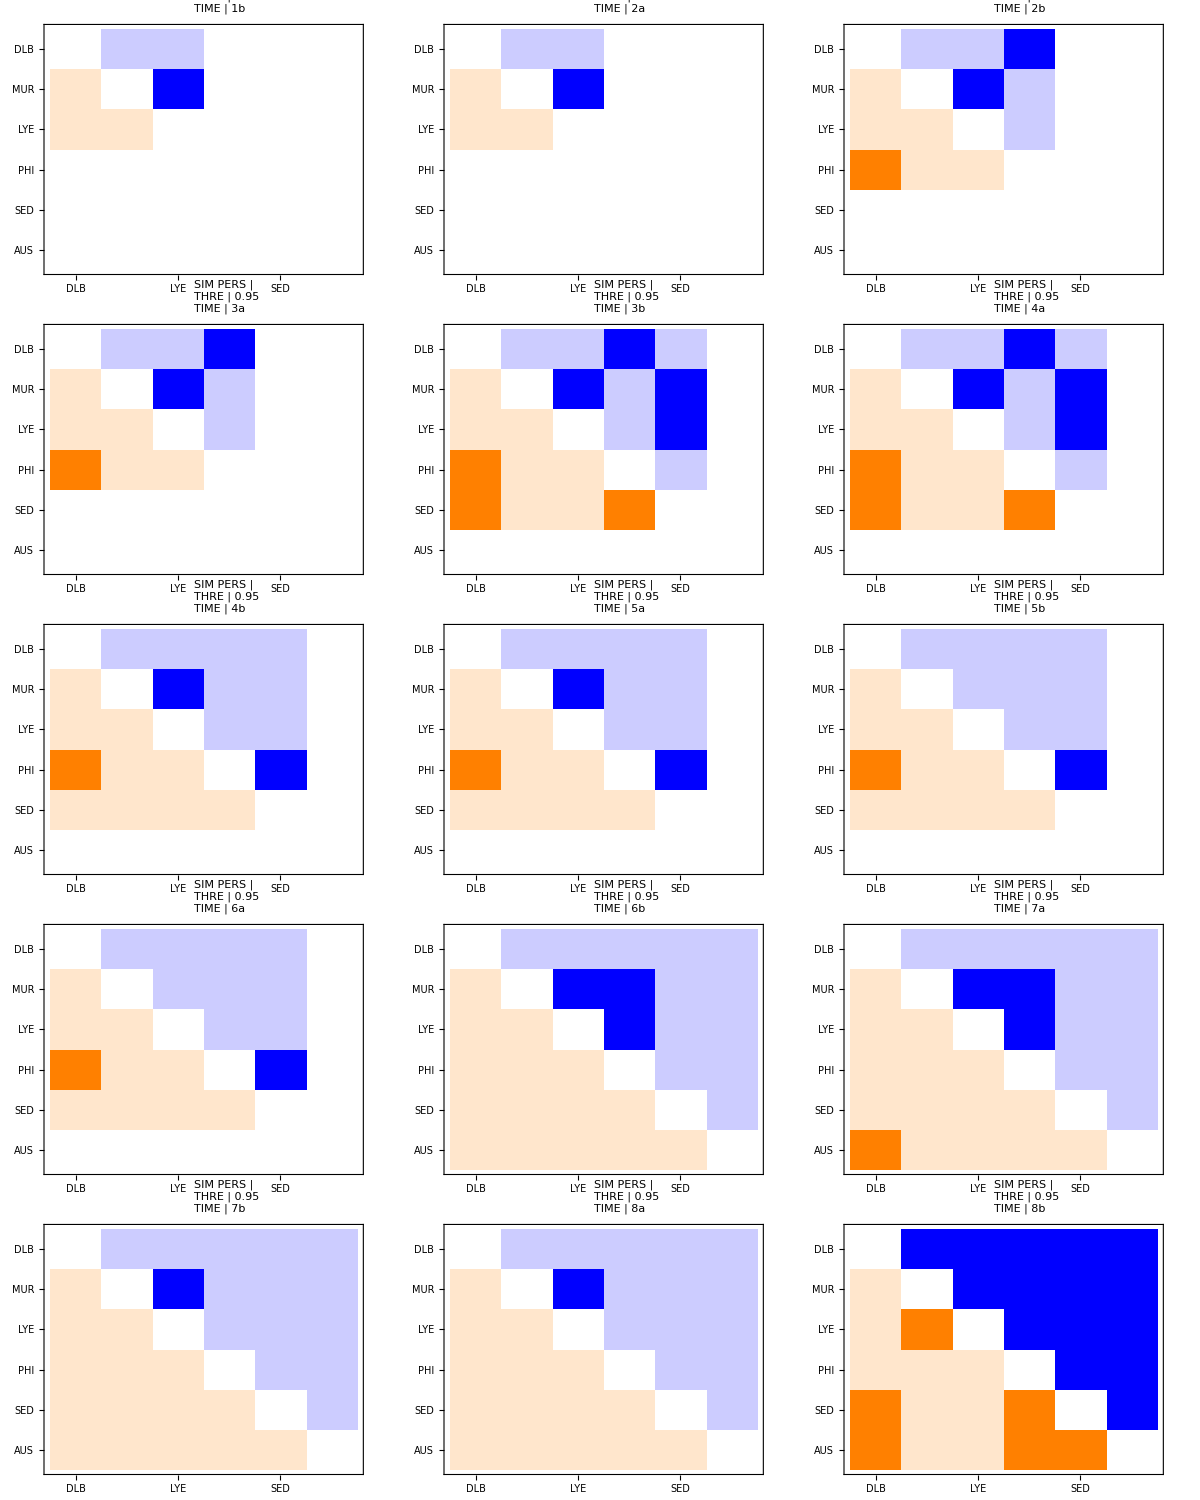

```mathematica
(*dataH,dataE,names, len, dataMin, dataMax*)
threshold=0.95;
plotsS=groupingEndoTot[dataH,dataE, len,names, dataMin,dataMax, threshold];
plotsGrid=Grid[{plotsS[[1;;3]],plotsS[[4;;6]],plotsS[[7;;9]],plotsS[[10;;12]],plotsS[[13;;15]]},ItemSize->35]
```

```mathematica
SetDirectory["/home/carla/GDC/Comparisons/New_REKO_19_02_21/Persons/Groups_ENDO/Threshold_"<>StringReplace[ToString[threshold],"."->"_"]]
```

/home/carla/GDC/Comparisons/New_REKO_19_02_21/Persons/Groups_ENDO/Threshold_0_95

```mathematica
Export["gdc_GROUPS_PERS_ENDO_"<>StringReplace[ToString[threshold],"."->"_"]<>"_grid.jpeg",plotsGrid,ImageResolution->200]
(*Map[Export["gdc_GROUPS_PERS_ENDO_"<>StringReplace[ToString[threshold],"."->"_"]<>"_S"<>ToString[tsStr[[#]]]<>".jpeg",plotsS[[#]],ImageResolution->200]&,Range[Length[tsStr]]]*)
```

gdc_GROUPS_PERS_ENDO_0_95_grid.jpeg